## 5. Supervised learning: Prediction

Aim: Train a model to predict a numerical response y for unseen data. Use a training set consisting of N_T training examples with known values for y.

Use a trained model to

Predict numerical values based on numerical or categorical data

Each example is a vector x of M numerical features, {x_1,x_2,...,x_M}

Implemented in Wolfram Language with the function Predict

Predict the next value in a sequence

Function SequencePredict

## 5.1 Predicting numerical values

This section explains the basic usage of the Predict function. Basic concepts will be illustrated by means of a simple example. An example using real data will be given at the end of this chapter and another example will be covered (by you) in practicals.

### A simple example

#### The data

Consider a small training dataset in which a variable y (to be predicted) depends on a numerical variable x.

We consider the following small training set with format giving the value of y for several values of x (format x→ y)

```mathematica
trainingset={1-> 12.9,2-> 8.2,3-> 6.9,4-> 3.1};
```

The data can be easily visualised in a scatterplot.

Before doing the scatterplot, we need to convert the trainingset into a list to be plotted with ListPlot.

Aside:
One can transform trainingset into the list we need in several ways:

Extracting elements from trainingset and creating a list with {x,y} for each data point.

```mathematica
Transpose[{trainingset[[All,1]],trainingset[[All,2]]}]
```

{{1,12.9},{2,8.2},{3,6.9},{4,3.1}}

Transform trainingset into a list would use Keys, Values and Transpose. Feel free to use the way you find more intuitive. This might include ways that I didn’t explain.

```mathematica
trainingset
```

{1→12.9,2→8.2,3→6.9,4→3.1}

```mathematica
Keys[trainingset]
```

{1,2,3,4}

```mathematica
Values[trainingset]
```

{12.9,8.2,6.9,3.1}

```mathematica
Transpose[{Keys[trainingset],Values[trainingset]}]
```

{{1,12.9},{2,8.2},{3,6.9},{4,3.1}}

Use Apply and List functions.

You probably saw how to use Apply in other courses of the programme but let us remind ourselves how it works. Consider the following example:

```mathematica
Apply[f,{1->a,2->b,3->c}]
```

f[1→a,2→b,3→c]

Alternatively, one can use @@:

```mathematica
f@@{1->a,2->b,3->c}
```

f[1→a,2→b,3→c]

In this way, the function f is applied to the whole list. However, we want to apply it to each element of the list. This can be done by specifying that we want to apply it al level {1} of the list as follows:

```mathematica
Apply[f,{1->a,2->b,3->c},{1}]
```

{f[1,a],f[2,b],f[3,c]}

Alternatively,

```mathematica
f@@@{1->a,2->b,3->c}
```

{f[1,a],f[2,b],f[3,c]}

Going back to our trainingset:

```mathematica
Apply[List,trainingset,{1}]
```

{{1,12.9},{2,8.2},{3,6.9},{4,3.1}}

or

```mathematica
List@@@trainingset
```

{{1,12.9},{2,8.2},{3,6.9},{4,3.1}}

Back to the scatterplot
One way or another, one obtains the following scatterplot for the training data

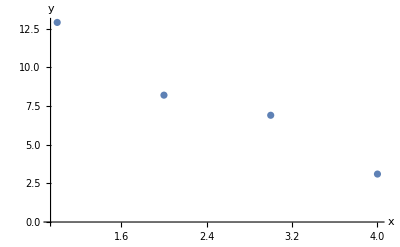

```mathematica
listtrainigset=List@@@trainingset;
ListPlot[listtrainigset,AxesLabel->{"x","y"}]
```

The scatterplot seems to suggest that it should be possible to predict, for example, a value of y for x = 3.5 which was not seen in the training dataset. One can do this by training a predictor (note the difference with the term “classifier” used in previous sections for classification models).

#### Training a predictor

Use the Predict function to train a predictor using trainingset:

```mathematica
p=Predict[trainingset]
```

PredictorFunction[…]

Predict works for prediction in an analogous way as Classify for classification.

The prediction of the trained predictor is a numerical value (not a class):

```mathematica
prediction=p[3.5]
```

5.

#### Predictor performance - How good is the prediction?

Predictions are real numbers, not classes

In contrast to classification, one cannot simply check it the result is in the expected class.

If our dataset is large, one could split it into training and test datasets as we did for classification.

If the training dataset is small, splitting it into training and test datasets might not be possible. 

In simple cases, one can plot together the training data and prediction on a scatterplot :

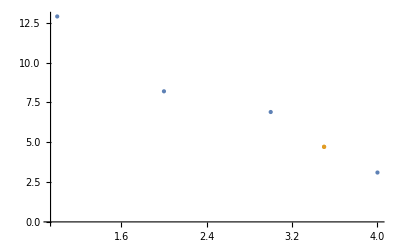

```mathematica
ListPlot[{listtrainigset,{{3.5,prediction}}},PlotStyle->PointSize[Large]]
```

The prediction might not look very accurate but, in fact, the predictor does not only give a point estimate but it gives a distribution for the predicted value

```mathematica
dist=p[3.5,"Distribution"]
```

NormalDistribution[5.,2.54865]

Have a look at the pdf for the predicted distribution:

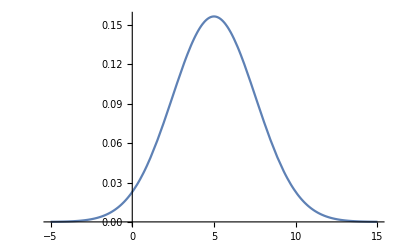

```mathematica
Plot[PDF[dist,x],{x,-5,15}]
```

In order to set the horizontal axis range without having to guess the values for x, one can use the mean and standard deviation of the distribution as follows:

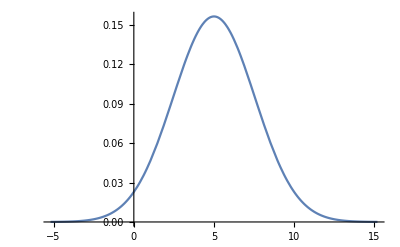

```mathematica
Plot[PDF[dist,x],{x,Mean[dist]-4 StandardDeviation[dist],Mean[dist]+4 StandardDeviation[dist]},PlotRange->All]
```

In this way, you can easily plot the PDF for any normally distributed random variable, irrespective of they mean and standard deviation.

The value found above for the prediction variable is just the expected value of the predicted distribution:

```mathematica
Mean[dist]
```

5.

but the prediction has some uncertainty which can be estimated in terms of the standard deviation:

```mathematica
StandardDeviation[dist]
```

2.54865

If the uncertainty of the prediction is taken into account, it looks reasonable when compared with the training data.

Here, I consider one standard deviation (68% of chances that the prediction will fall within this range)

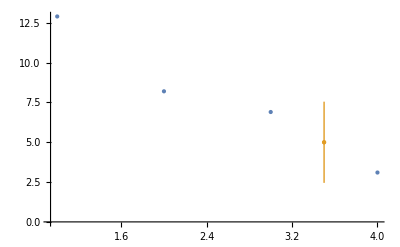

```mathematica
ListPlot[{listtrainigset,{{3.5,Around[Mean[dist],StandardDeviation[dist]]}}},PlotStyle->PointSize[Large],PlotRange->All]
```

One can plot the dispersion of predictions together with the straight line giving the mean value of the prediction. It can be convenient to define a function to do this:

```mathematica
plotSDRegion[predictor_,data_,xmin_,xmax_]:=Module[{p=predictor,data0=data,xmin0=xmin,xmax0=xmax,x},
Show[Plot[{p[x],
p[x]+StandardDeviation[p[x,"Distribution"]],p[x]-StandardDeviation[p[x,"Distribution"]]},
{x,xmin0,xmax0},
PlotStyle->{Blue,Gray,Gray},
Filling->{2->{3}},PlotLegends->{"Prediction","Confidence Interval"}],ListPlot[data0,PlotStyle->Red,PlotLegends->{"Data"}]]]
```

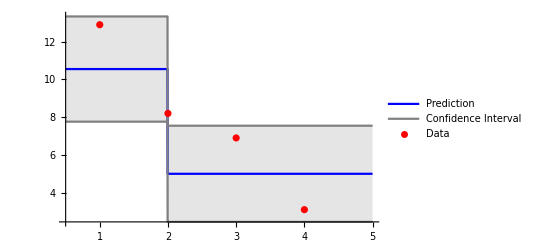

```mathematica
plotSDRegion[p,listtrainigset,0.5,5]
```

### Methods for prediction

Several methods can be used for prediction of numerical values. Some of the most widely used are:

Linear regression

Nearest neighbours: Similar idea to KNN method in

Decision tree: Used both for classification and prediction.

Neural network: Later...

Other implemented in Mathematica: “GradientBoostedTrees”, “RandomForest” , “GaussianProcess”

One can specify a method in the Predict function as follows: 

Predict[training data, Method→ "method name"]

As for classification, if no method is specified, Mathematica will try several and present results for the method with lowest cost function.

### Linear regression

#### General formulation

Features: Suppose that we have a data set in which instances are characterised by M numerical features: x = {x_1,x_2,...,x_M}

Dependent variable: For each example in the data set, we are also given a variable y that depends on the features, x.

Aim: Given an unseen example with feature vector x', we want to predict the value corresponding to the dependent variable, y.

Two assumption:

The dependent variable can be expressed as a linear combination of the features:

y=f(x; w_0,w)≡w_0+w_1 x_1+w_2 x_2+....+w_M x_M+ϵ

This can also be written with more compact notations as	
	 f(x; w_0,w)=w_0+∑_(i=1)^M w_i x_i+ϵ=w_0+w^T x +ϵ, 	      w^T=(w_1,w_2,...,w_M),  x=(x_1
x_2
...
x_M)

Here,

w_0 is the intercept

{w_1,w_2,...,w_M} are the weight of each feature to explain the dependent variable y

ϵ is the residual error between the linear prediction and the true response

The residual error is often assumed to obey a normal distribution:

ϵ~N(μ,σ^2)

#### Fitting the model to data

To train a linear model from data, we need to find the values of the parameters {w_0,w_1,w_2,...,w_M} and the distribution for ϵ that gives the better fit of the model to the data.

For 1-dimensional data (one feature, M = 1), we just need to find the straight line that is closest to all the points in the training dataset.

In other words, the line f(x; w_0,w) for which the distance of the data to the line is minimized.

```mathematica
fline[x_,w0_,w1_]:=w0+w1 x;

Manipulate[Show[Plot[fline[x,w0,w1],
{x,0.5,5},
PlotStyle->{Blue},PlotLegends->{"Prediction, f(x)"},PlotRange->{{0.5,5},{0,13.5}}],ListPlot[listtrainigset,PlotStyle->Red,PlotLegends->{"Data"}]],{w0,5,13},{w1,-2,2}]
```

ListPlot::lpn: listtrainigset is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[listtrainigset,PlotStyle→RGBColor[1, 0, 0],PlotLegends→{Data}]].

ListPlot::lpn: listtrainigset is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[listtrainigset,PlotStyle→RGBColor[1, 0, 0],PlotLegends→{Data}]].

I can get predictions with the linear regression model by setting this in the Predict function as follows:

```mathematica
p=Predict[trainingset,Method-> "LinearRegression"]
```

PredictorFunction[…]

Predicted value for x = 3.5:

```mathematica
p[3.5]
```

4.71332

The prediction obeys a normal distribution (in fact, this is one of the hypotheses of the linear regression model):

```mathematica
p[3.5,"Distribution"]
```

NormalDistribution[4.71332,0.986633]

We can use the plotSDRegion function defined before to see the prediction for the uncertainty of a range of values of x. As expected, linear regression predicts a mean (blue line) that decreases linearly with x. The dispersion or predicted standard devia

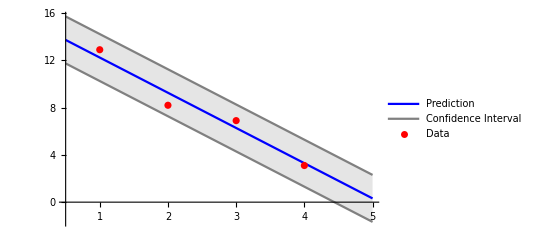

```mathematica
plotSDRegion[p,listtrainigset,0.5,5]
```

#### Loss function (or cost function)

A cost function measures how far away a mathematical model is from the data.

In linear regression, one adjusts the parameters {w_0,w} to minimise the cost function.

The Predict function uses the mean cross entropy for the linear regression model:

```mathematica
Information[p,"MeanCrossEntropy"]
```

3.00.8

#### Using linear model fit function

As shown above, Wolfram Language can be used to train a predictor based on the linear regression model.

A linear model can also be fitted using the LinearModelFit function with the following syntax:

LinearModelFit[{y^(1),y^(2),...,y^(n)},{x_1,x_2,...,x_M},x]

For the 1 dimensional example analysed above,

```mathematica
lm=LinearModelFit[listtrainigset,x,x]
```

FittedModel[15.45-3.07 x]

```mathematica
Information[p,"Function"]
```

15.2181-2.98025 #1&

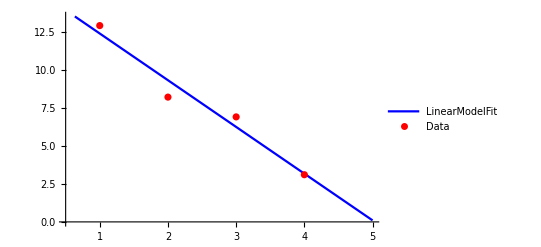

```mathematica
Show[Plot[{lm[x]},
{x,0.5,5},
PlotStyle->{Blue},PlotLegends->{"LinearModelFit"},PlotRange->{{0.5,5},{0,13.5}}],ListPlot[listtrainigset,PlotStyle->Red,PlotLegends->{"Data"}]]
```

We can compare the line obtained with the Predict  function and the one obtained with LinearModelFit

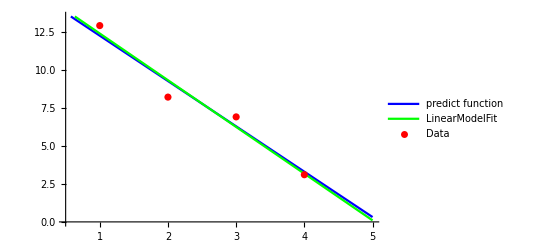

```mathematica
Show[Plot[{p[x],lm[x]},
{x,0.5,5},
PlotStyle->{Blue,Green},PlotLegends->{"predict function","LinearModelFit"},PlotRange->{{0.5,5},{0,13.5}}],ListPlot[listtrainigset,PlotStyle->Red,PlotLegends->{"Data"}]]
```

#### Cost function for LinearModelFit

The cost function used by the LinearModelFit function is a classical. It is the sum of the residuals measuring the distance between the points and the linear function.

In one dimension:

```mathematica
fline[x_,w0_,w1_]:=w0+w1 x;

Manipulate[Show[Plot[fline[x,w0,w1],
{x,0.5,5},
PlotStyle->{Blue},PlotLegends->{"Prediction, f(x)"},PlotRange->{{0.5,5},{0,13.5}}],ListPlot[listtrainigset,PlotStyle->Red,PlotLegends->{"Data"}],Table[Graphics[Line[{{listtrainigset[[i,1]],fline[listtrainigset[[i,1]],w0,w1]},listtrainigset[[i]]}]],{i,1,Length[listtrainigset]}]],{w0,5,18},{w1,-4,3}]
```

ListPlot::lpn: listtrainigset is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[listtrainigset,PlotStyle→RGBColor[1, 0, 0],PlotLegends→{Data}],{}].

ListPlot::lpn: listtrainigset is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[listtrainigset,PlotStyle→RGBColor[1, 0, 0],PlotLegends→{Data}],{}].

ListPlot::lpn: listtrainigset is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[listtrainigset,PlotStyle→RGBColor[1, 0, 0],PlotLegends→{Data}],{}].

Residuals for an arbitrary line in this case are given by the black lines.

What are the residuals for our 1D example?

```mathematica
residuals=lm["FitResiduals"]
```

{0.52,-1.11,0.66,-0.07}

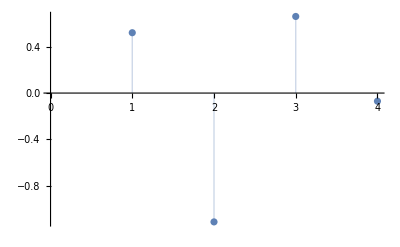

```mathematica
ListPlot[residuals, Filling->Axis]
```

The cost function is then the sum of the square of residuals:

```mathematica
Total[residuals^2]
```

1.943

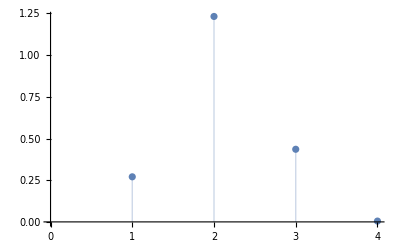

```mathematica
ListPlot[residuals^2, Filling->Axis]
```

```mathematica
Total[residuals]
```

4.44089×10^-16

A perfect fit would give a zero cost.

In M dimensions: Suppose that you have a training dataset with N data points {x^(1),x^(2),...,x^(N)} with M features each. Each example carries a numerical value,  {y^(1),y^(2),...,y^(N)}. More explicitly, the data set can be viewed as follows:

x_1^(1) | x_2^(1) | ... | x_M^(1) | y^(1)
x_1^(2) | x_2^(2) | ... | x_M^(2) | y^(2)
... | ... | ... | ... | ...
x_1^(N) | x_2^(N) | ... | x_M^(N) | y^(N)

We fit a linear model f(x) to the data. The general expression for the quadratic distance cost function is

J(w_0,w)=1/(2N)∑_(n=1)^N (f(x^(n);w_0,w)-y^(n))^2

### Information on predictors

#### Predictor information

```mathematica
Information[p]
```

Predictor information
Data type | Numerical
Standard deviation | 3.28 ± 1.
Method | LinearRegression
Single evaluation time | 3.54 ms/example
Batch evaluation speed | 50.2 examples/ms
Loss | 3.04 ± 0.77
Model memory | 172. kB
Training examples used | 4 examples
Training time | 1.18 s

#### Training progress reporting

One can show information for the training progress in several ways - This also works for Classify

By default, the simple panel is used:

```mathematica
Predict[trainingset,Method->"LinearRegression",TrainingProgressReporting->"SimplePanel"]
```

PredictorFunction[…]

```mathematica
Predict[trainingset,TrainingProgressReporting->"Print"]
```

| Time elapsed: | Training example used: | Current best method: | Standard deviation: | Current loss: |

|    0.821s     |          3/4           |     DecisionTree     |        3.21         |     2.58      |

PredictorFunction[…]

#### Properties of predictors

One can get information on trained predictors in a similar way as for classifiers trained with Classify

```mathematica
Information[p,"Properties"]
```

{BatchEvaluationSpeed,BatchEvaluationTime,DistributionFunction,EvaluationTime,ExampleNumber,FeatureNames,FeatureNumber,FeatureTypes,Function,FunctionMemory,FunctionProperties,IndeterminateThreshold,L1Regularization,L2Regularization,LearningCurve,MaxTrainingMemory,MeanCrossEntropy,Method,MethodDescription,MethodOption,OptimizationMethod,PerformanceGoal,Properties,StandardDeviation,TrainingTime,UtilityFunction}

```mathematica
Information[p,"Method"]
```

LinearRegression

```mathematica
Information[p,"MethodDescription"]
```

The linear regression predictor predicts values with a linear combination of the features.

```mathematica
pfunction=Information[p,"Function"]
```

15.4023-3.05399 #1&

```mathematica
pfunction[x]
```

15.4023-3.05399 x

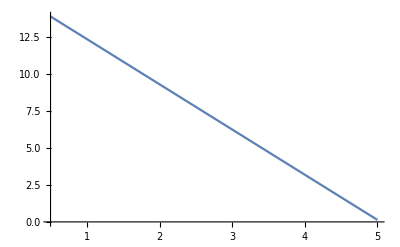

```mathematica
Plot[pfunction[x],{x,0.5,5}]
```

```mathematica
Information[p,"LearningCurve"]
```

Some details (not crucial for the course): In the “learning curves for all algorithms” panel, we see that Mathematica tried several models for prediction despite the fact that we set it to use “LinearRegression” method. In fact, all the models are linear regression but the loss function used to obtain each of them is slightly different. Costs functions differ in the regularization term that is added to the normal loss function, J. For 1-dimensional data (i.e. one feature per example), the regularized loss function is:

J_r(w_0,w_1)=J(w_0,w_1)+λ_1|w_1|+λ_2/2 w_1^2
In Mathematica, the regularization parameter λ_1 is indicated as “L1Regularization” (set as 0 by default) and λ_2 as “L2Regularization”.

### Nearest neighbours method

#### How does it work?

Suppose that we want to predict the value of y for a point with feature vector x={x_1,x_2,...,x_M} (i.e. in general each example is characterised by M features).

Fix a number of neighbours k

Select k nearest points to x in the training data set {x^(1),x^(2),...,x^(N)}. Suppose that the nearest neighbours are {z_1,z_2,...,z_k}

The prediction for y is the mean value of the features of the nearest k neighbours: 

y=Mean[{z_1,z_2,...,z_k}]

#### Training a predictor

```mathematica
pNN=Predict[trainingset,Method->{"NearestNeighbors","NeighborsNumber"-> 2}]
```

PredictorFunction[…]

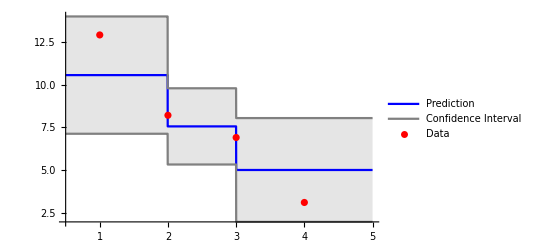

```mathematica
plotSDRegion[pNN,listtrainigset,0.5,5]
```

For instance, the prediction for a point with x = 1.2 is given by the mean of the value of y of the neighbours.

For k = 2, the neighbours are

```mathematica
listtrainigset[[1;;2,2]]
```

{12.9,8.2}

And the prediction is

```mathematica
Mean[listtrainigset[[1;;2,2]]]
```

10.55

Indeed:

```mathematica
pNN[1.2]
```

10.55

```mathematica
pNN[3.5]
```

5.

### Decision tree

Decision trees can be used for both classification and prediction.

A decision tree is a flow chart–like structure in which each internal node represents a “test” on a feature, each branch represents the outcome of the test, and each leaf represents a class distribution, value distribution or probability density.

#### Decision tree for classification

Decision trees are easy to understand intuitively. A classification example to get the idea: Have you played “Guess Who” or the 20 questions game?

“Guess who” is played by two players. Each player gets a random picture from a character. The goal is to guess the name of the character chosen by your opponent. This is done by asking questions in turn to infer the features of your opponent’s character. Typical questions are:

Is he/she blonde?

Is male or female?

Does he have a beard?

...

#### Decision tree for prediction - Regression tree

For prediction, a decision tree is built to partition the data in such a way that predictions are made in a piecewise manner.

Let us see what Mathematica gives for our simple example when setting the method to decision tree.

```mathematica
pDT=Predict[trainingset,Method->"DecisionTree"]
```

PredictorFunction[…]

```mathematica
plotSDRegion[pDT,listtrainigset,0.5,5]
```

-Graphics-

In this case, it is similar to the nearest neighbours method but not identical.

```mathematica
pDT[1.8]
```

10.55

```mathematica
pDT[3.5]
```

5.

A regression tree looks like this:

-Graphics-

Vertices in the tree are questions to the data (i.e. whether an example has a feature below or above a partition point s).

The leaf parameters are values of the response variable corresponding to the data in each vertex.

**Warning**: The following description is given for students interested in deeper understanding of algorithms. It is not considered to be a core part of the course

More formally, the algorithm to partition the data into two subsets works as follows. Let us consider a dataset with N examples {(x_1,y_1),(x_2,y_2),...,(x_N,y_N)}.

1. Split the data into two sets depending on the value of x

Ω_L(s)={l|x_l≤s} : Examples in the dataset with a features x_l≤s.

Ω_R(s)={r|x_r>s} : Examples in the dataset with a features x_r>s.

These define two branches in the tree.

2. Approximate the response variable y in each branch by the mean value of the response variables in each branch, i.e. by the leaf variables 

v_1=1/(|Ω_L|)∑_(l∈Ω_L) y_l

v_2=1/(|Ω_R|)∑_(r∈Ω_R) y_r

3. Consider a loss function giving the quadratic distance from the data in each branch to the leaf variable in the branch, i.e.

J(s)=∑_(l∈Ω_L) (y_l-v_1)^2+∑_(r∈Ω_R) (y_r-v_2)^2

4. Find the optimal value s^* of the partition parameter s by minimising the cost function, i.e.

s^*=argmin_s{J(s)}

5. One could do more partitions of the data by defining a tree with more branches. 

-Graphics-

We need a criterion to stop the partitioning of the data. A typical criterion consists in stopping when a new partition does not decrease the loss function more than a certain value (set by us). Alternatively, we can stop when the number of partitions reaches a maximum (also set by us).

Here, I have focused on data with a single feature (i.e. 1-dimensional data). These methods, however, can be generalised to data with multiple features. 

If interested, see more information in (not required for the course):

Chapter 14 of Jeremy Watt, Reza Borhani, Aggelos K. Katsaggelos “Machine Learning Refined: Foundations, Algorithms, and Applications” Cambridge University Press, 2nd Edition (2020).

Chapter 16 of Kevin P. Murphy “Machine Learning: A Probabilistic Perspective” The MIT Press (2012).

** Back to less mathematical contents. **

Description of the algorithm for our example.

Recall the data:

```mathematica
listtrainigset
```

{{1,12.9},{2,8.2},{3,6.9},{4,3.1}}

Values of x and y:

```mathematica
xval=listtrainigset[[All,1]]
```

{1,2,3,4}

```mathematica
yval=listtrainigset[[All,2]]
```

{12.9,8.2,6.9,3.1}

For s=2:

Ω_L(2)={1,2}  and Ω_R(2)={3,4}

```mathematica
s=2;
```

```mathematica
omegaL=Position[xval,_?(#≤s&)]//Flatten   (* Here, "?" corresponds to the PatternTest function in Mathematica. We want to test on whether the elements of xval satisfy #≤s. See documentation for PatternTest if in doubt.*)
v1=Mean[yval[[omegaL]]]
```

{1,2}

10.55

```mathematica
omegaR=Position[xval,_?(#>s&)]//Flatten 
v2=Mean[yval[[omegaR]]]
```

{3,4}

5.

Loss function:

```mathematica
Jloss=Total[(yval[[omegaL]]-v1)^2]+Total[(yval[[omegaR]]-v2)^2]
```

18.265

One can try for s = 1,2,3,4 and check that s = 2 gives the smallest loss.

#### Tasks for you

Task 1. (Hard) Although it is not necessary to program methods from scratch (i.e. no need to reinvent the wheel), if interested, build a function to implement the regression tree method for generic 1-dimensional data from scratch.

### Example: Predicting the price of houses

We will now look at a classical ML prediction example which trains a model to predict the price of houses based on 13 input variables for houses in a training set. The dataset is a bit old (from 1980) but it is a very useful example to illustrate prediction methods.

#### The data

```mathematica
ExampleData[{"MachineLearning","BostonHomes"},"Source"]
```

Belsley D. A., Kuh, E. and Welsch, R. E. (1980) Regression Diagnostics. Identifying Influential Data and Sources of Collinearity. New York: Wiley.

```mathematica
ExampleData[{"MachineLearning","BostonHomes"},"LongDescription"]
```

Home values for 506 Boston suburbs with potential influential factors (such as the crime rate, number of rooms, distance to employment centers, etc.).

	The test and training sets were obtained by creating a random sample of 30% of the data for the test set, using the rest for training.

```mathematica
description=ExampleData[{"MachineLearning","BostonHomes"},"VariableDescriptions"];
TableForm[description[[1]]]
```

Per capita crime rate by town
Proportion of residential land zoned for lots over 25000 square feet
Proportion of non-retail business acres per town
Charles River dummy variable (1 if tract bounds river, 0 otherwise)
Nitrogen oxide concentration (parts per 10 million)
Average number of rooms per dwelling
Proportion of owner-occupied units built prior to 1940
Weighted mean of distances to five Boston employment centers
Index of accessibility to radial highways
Full-value property-tax rater per $10000
Pupil-teacher ratio by town
1000(Bk-0.63)^2 where Bk is the proportion of blacks by town
Lower status of the population (percent)
Median value of owner-occupied homes in $1000s

#### Training a predictor

```mathematica
bhtraining=ExampleData[{"MachineLearning","BostonHomes"},"TrainingData"];
```

```mathematica
Length[bhtraining]
```

338

```mathematica
bhtraining[[1]]
```

{0.02731,0,7.07,0,0.469,6.421,78.9,4.9671,2,242,17.8,396.9,9.14}→21.6

```mathematica
bhtraining
```

{{0.02731,0,7.07,0,0.469,6.421,78.9,4.9671,2,242,17.8,396.9,9.14}→21.6,{0.02729,0,7.07,0,0.469,7.185,61.1,4.9671,2,242,17.8,392.83,4.03}→34.7,{0.03237,0,2.18,0,0.458,6.998,45.8,6.0622,3,222,18.7,394.63,2.94}→33.4,{0.14455,12.5,7.87,0,0.524,6.172,96.1,5.9505,5,311,15.2,396.9,19.15}→27.1,{0.21124,12.5,7.87,0,0.524,5.631,100,6.0821,5,311,15.2,386.63,29.93}→16.5,{0.22489,12.5,7.87,0,0.524,6.377,94.3,6.3467,5,311,15.2,392.52,20.45}→15,{0.11747,12.5,7.87,0,0.524,6.009,82.9,6.2267,5,311,15.2,396.9,13.27}→18.9,{0.09378,12.5,7.87,0,0.524,5.889,39,5.4509,5,311,15.2,390.5,15.71}→21.7,{0.63796,0,8.14,0,0.538,6.096,84.5,4.4619,4,307,21,380.02,10.26}→18.2,{0.62739,0,8.14,0,0.538,5.834,56.5,4.4986,4,307,21,395.62,8.47}→19.9,{1.05393,0,8.14,0,0.538,5.935,29.3,4.4986,4,307,21,386.85,6.58}→23.1,{0.7842,0,8.14,0,0.538,5.99,81.7,4.2579,4,307,21,386.75,14.67}→17.5,{0.80271,0,8.14,0,0.538,5.456,36.6,3.7965,4,307,21,288.99,11.69}→20.2,{1.25179,0,8.14,0,0.538,5.57,98.1,3.7979,4,307,21,376.57,21.02}→13.6,{0.85204,0,8.14,0,0.538,5.965,89.2,4.0123,4,307,21,392.53,13.83}→19.6,{1.23247,0,8.14,0,0.538,6.142,91.7,3.9769,4,307,21,396.9,18.72}→15.2,{0.98843,0,8.14,0,0.538,5.813,100,4.0952,4,307,21,394.54,19.88}→14.5,{0.84054,0,8.14,0,0.538,5.599,85.7,4.4546,4,307,21,303.42,16.51}→13.9,{0.67191,0,8.14,0,0.538,5.813,90.3,4.682,4,307,21,376.88,14.81}→16.6,{0.95577,0,8.14,0,0.538,6.047,88.8,4.4534,4,307,21,306.38,17.28}→14.8,{1.00245,0,8.14,0,0.538,6.674,87.3,4.239,4,307,21,380.23,11.98}→21,{1.13081,0,8.14,0,0.538,5.713,94.1,4.233,4,307,21,360.17,22.6}→12.7,{1.35472,0,8.14,0,0.538,6.072,100,4.175,4,307,21,376.73,13.04}→14.5,{1.15172,0,8.14,0,0.538,5.701,95,3.7872,4,307,21,358.77,18.35}→13.1,{1.61282,0,8.14,0,0.538,6.096,96.9,3.7598,4,307,21,248.31,20.34}→13.5,{0.08014,0,5.96,0,0.499,5.85,41.5,3.9342,5,279,19.2,396.9,8.77}→21,{0.03359,75,2.95,0,0.428,7.024,15.8,5.4011,3,252,18.3,395.62,1.98}→34.9,{0.12744,0,6.91,0,0.448,6.77,2.9,5.7209,3,233,17.9,385.41,4.84}→26.6,{0.15936,0,6.91,0,0.448,6.211,6.5,5.7209,3,233,17.9,394.46,7.44}→24.7,{0.12269,0,6.91,0,0.448,6.069,40,5.7209,3,233,17.9,389.39,9.55}→21.2,{0.17142,0,6.91,0,0.448,5.682,33.8,5.1004,3,233,17.9,396.9,10.21}→19.3,{0.18836,0,6.91,0,0.448,5.786,33.3,5.1004,3,233,17.9,396.9,14.15}→20,{0.22927,0,6.91,0,0.448,6.03,85.5,5.6894,3,233,17.9,392.74,18.8}→16.6,{0.25387,0,6.91,0,0.448,5.399,95.3,5.87,3,233,17.9,396.9,30.81}→14.4,{0.08873,21,5.64,0,0.439,5.963,45.7,6.8147,4,243,16.8,395.56,13.45}→19.7,{0.04337,21,5.64,0,0.439,6.115,63,6.8147,4,243,16.8,393.97,9.43}→20.5,{0.0536,21,5.64,0,0.439,6.511,21.1,6.8147,4,243,16.8,396.9,5.28}→25,{0.04981,21,5.64,0,0.439,5.998,21.4,6.8147,4,243,16.8,396.9,8.43}→23.4,{0.0136,75,4,0,0.41,5.888,47.6,7.3197,3,469,21.1,396.9,14.8}→18.9,{0.02055,85,0.74,0,0.41,6.383,35.7,9.1876,2,313,17.3,396.9,5.77}→24.7,{0.01432,100,1.32,0,0.411,6.816,40.5,8.3248,5,256,15.1,392.9,3.95}→31.6,{0.15445,25,5.13,0,0.453,6.145,29.2,7.8148,8,284,19.7,390.68,6.86}→23.3,{0.14932,25,5.13,0,0.453,5.741,66.2,7.2254,8,284,19.7,395.11,13.15}→18.7,{0.17171,25,5.13,0,0.453,5.966,93.4,6.8185,8,284,19.7,378.08,14.44}→16,{0.11027,25,5.13,0,0.453,6.456,67.8,7.2255,8,284,19.7,396.9,6.73}→22.2,{0.1265,25,5.13,0,0.453,6.762,43.4,7.9809,8,284,19.7,395.58,9.5}→25,{0.03584,80,3.37,0,0.398,6.29,17.8,6.6115,4,337,16.1,396.9,4.67}→23.5,{0.13554,12.5,6.07,0,0.409,5.594,36.8,6.498,4,345,18.9,396.9,13.09}→17.4,{0.12816,12.5,6.07,0,0.409,5.885,33,6.498,4,345,18.9,396.9,8.79}→20.9,{0.08826,0,10.81,0,0.413,6.417,6.6,5.2873,4,305,19.2,383.73,6.72}→24.2,{0.15876,0,10.81,0,0.413,5.961,17.5,5.2873,4,305,19.2,376.94,9.88}→21.7,{0.07896,0,12.83,0,0.437,6.273,6,4.2515,5,398,18.7,394.92,6.78}→24.1,{0.09512,0,12.83,0,0.437,6.286,45,4.5026,5,398,18.7,383.23,8.94}→21.4,{0.10153,0,12.83,0,0.437,6.279,74.5,4.0522,5,398,18.7,373.66,11.97}→20,{0.08707,0,12.83,0,0.437,6.14,45.8,4.0905,5,398,18.7,386.96,10.27}→20.8,{0.04113,25,4.86,0,0.426,6.727,33.5,5.4007,4,281,19,396.9,5.29}→28,{0.03551,25,4.86,0,0.426,6.167,46.7,5.4007,4,281,19,390.64,7.51}→22.9,{0.05059,0,4.49,0,0.449,6.389,48,4.7794,3,247,18.5,396.9,9.62}→23.9,{0.05188,0,4.49,0,0.449,6.015,45.1,4.4272,3,247,18.5,395.99,12.86}→22.5,{0.05302,0,3.41,0,0.489,7.079,63.1,3.4145,2,270,17.8,396.06,5.7}→28.7,{0.04684,0,3.41,0,0.489,6.417,66.1,3.0923,2,270,17.8,392.18,8.81}→22.6,{0.02875,28,15.04,0,0.464,6.211,28.9,3.6659,4,270,18.2,396.33,6.21}→25,{0.11504,0,2.89,0,0.445,6.163,69.6,3.4952,2,276,18,391.83,11.34}→21.4,{0.12083,0,2.89,0,0.445,8.069,76,3.4952,2,276,18,396.9,4.21}→38.7,{0.08187,0,2.89,0,0.445,7.82,36.9,3.4952,2,276,18,393.53,3.57}→43.8,{0.0686,0,2.89,0,0.445,7.416,62.5,3.4952,2,276,18,396.9,6.19}→33.2,{0.11432,0,8.56,0,0.52,6.781,71.3,2.8561,5,384,20.9,395.58,7.67}→26.5,{0.21161,0,8.56,0,0.52,6.137,87.4,2.7147,5,384,20.9,394.47,13.44}→19.3,{0.1396,0,8.56,0,0.52,6.167,90,2.421,5,384,20.9,392.69,12.33}→20.1,{0.13262,0,8.56,0,0.52,5.851,96.7,2.1069,5,384,20.9,394.05,16.47}→19.5,{0.1712,0,8.56,0,0.52,5.836,91.9,2.211,5,384,20.9,395.67,18.66}→19.5,{0.13117,0,8.56,0,0.52,6.127,85.2,2.1224,5,384,20.9,387.69,14.09}→20.4,{0.12802,0,8.56,0,0.52,6.474,97.1,2.4329,5,384,20.9,395.24,12.27}→19.8,{0.26363,0,8.56,0,0.52,6.229,91.2,2.5451,5,384,20.9,391.23,15.55}→19.4,{0.10793,0,8.56,0,0.52,6.195,54.4,2.7778,5,384,20.9,393.49,13}→21.7,{0.10084,0,10.01,0,0.547,6.715,81.6,2.6775,6,432,17.8,395.59,10.16}→22.8,{0.22212,0,10.01,0,0.547,6.092,95.4,2.548,6,432,17.8,396.9,17.09}→18.7,{0.17134,0,10.01,0,0.547,5.928,88.2,2.4631,6,432,17.8,344.91,15.76}→18.3,{0.15098,0,10.01,0,0.547,6.021,82.6,2.7474,6,432,17.8,394.51,10.3}→19.2,{0.13058,0,10.01,0,0.547,5.872,73.1,2.4775,6,432,17.8,338.63,15.37}→20.4,{0.07165,0,25.65,0,0.581,6.004,84.1,2.1974,2,188,19.1,377.67,14.27}→20.3,{0.09299,0,25.65,0,0.581,5.961,92.9,2.0869,2,188,19.1,378.09,17.93}→20.5,{0.15038,0,25.65,0,0.581,5.856,97,1.9444,2,188,19.1,370.31,25.41}→17.3,{0.09849,0,25.65,0,0.581,5.879,95.8,2.0063,2,188,19.1,379.38,17.58}→18.8,{0.16902,0,25.65,0,0.581,5.986,88.4,1.9929,2,188,19.1,385.02,14.81}→21.4,{0.88125,0,21.89,0,0.624,5.637,94.7,1.9799,4,437,21.2,396.9,18.34}→14.3,{0.34006,0,21.89,0,0.624,6.458,98.9,2.1185,4,437,21.2,395.04,12.6}→19.2,{1.19294,0,21.89,0,0.624,6.326,97.7,2.271,4,437,21.2,396.9,12.26}→19.6,{0.59005,0,21.89,0,0.624,6.372,97.9,2.3274,4,437,21.2,385.76,11.12}→23,{0.97617,0,21.89,0,0.624,5.757,98.4,2.346,4,437,21.2,262.76,17.31}→15.6,{0.55778,0,21.89,0,0.624,6.335,98.2,2.1107,4,437,21.2,394.67,16.96}→18.1,{0.32264,0,21.89,0,0.624,5.942,93.5,1.9669,4,437,21.2,378.25,16.9}→17.4,{0.54452,0,21.89,0,0.624,6.151,97.9,1.6687,4,437,21.2,396.9,18.46}→17.8,{1.62864,0,21.89,0,0.624,5.019,100,1.4394,4,437,21.2,396.9,34.41}→14.4,{3.32105,0,19.58,1,0.871,5.403,100,1.3216,5,403,14.7,396.9,26.82}→13.4,{4.0974,0,19.58,0,0.871,5.468,100,1.4118,5,403,14.7,396.9,26.42}→15.6,{2.33099,0,19.58,0,0.871,5.186,93.8,1.5296,5,403,14.7,356.99,28.32}→17.8,{1.6566,0,19.58,0,0.871,6.122,97.3,1.618,5,403,14.7,372.8,14.1}→21.5,{1.49632,0,19.58,0,0.871,5.404,100,1.5916,5,403,14.7,341.6,13.28}→19.6,{1.12658,0,19.58,1,0.871,5.012,88,1.6102,5,403,14.7,343.28,12.12}→15.3,{2.14918,0,19.58,0,0.871,5.709,98.5,1.6232,5,403,14.7,261.95,15.79}→19.4,{1.41385,0,19.58,1,0.871,6.129,96,1.7494,5,403,14.7,321.02,15.12}→17,{2.44668,0,19.58,0,0.871,5.272,94,1.7364,5,403,14.7,88.63,16.14}→13.1,{1.22358,0,19.58,0,0.605,6.943,97.4,1.8773,5,403,14.7,363.43,4.59}→41.3,{1.34284,0,19.58,0,0.605,6.066,100,1.7573,5,403,14.7,353.89,6.43}→24.3,{1.46336,0,19.58,0,0.605,7.489,90.8,1.9709,5,403,14.7,374.43,1.73}→50,{1.83377,0,19.58,1,0.605,7.802,98.2,2.0407,5,403,14.7,389.61,1.92}→50,{1.51902,0,19.58,1,0.605,8.375,93.9,2.162,5,403,14.7,388.45,3.32}→50,{2.24236,0,19.58,0,0.605,5.854,91.8,2.422,5,403,14.7,395.11,11.64}→22.7,{1.80028,0,19.58,0,0.605,5.877,79.2,2.4259,5,403,14.7,227.61,12.14}→23.8,{2.3004,0,19.58,0,0.605,6.319,96.1,2.1,5,403,14.7,297.09,11.1}→23.8,{2.3139,0,19.58,0,0.605,5.88,97.3,2.3887,5,403,14.7,348.13,12.03}→19.1,{0.09178,0,4.05,0,0.51,6.416,84.1,2.6463,5,296,16.6,395.5,9.04}→23.6,{0.06642,0,4.05,0,0.51,6.86,74.4,2.9153,5,296,16.6,391.27,6.92}→29.9,{0.0578,0,2.46,0,0.488,6.98,58.4,2.829,3,193,17.8,396.9,5.04}→37.2,{0.06588,0,2.46,0,0.488,7.765,83.3,2.741,3,193,17.8,395.56,7.56}→39.8,{0.09103,0,2.46,0,0.488,7.155,92.2,2.7006,3,193,17.8,394.12,4.82}→37.9,{0.10008,0,2.46,0,0.488,6.563,95.6,2.847,3,193,17.8,396.9,5.68}→32.5,{0.08308,0,2.46,0,0.488,5.604,89.8,2.9879,3,193,17.8,391,13.98}→26.4,{0.06047,0,2.46,0,0.488,6.153,68.8,3.2797,3,193,17.8,387.11,13.15}→29.6,{0.05602,0,2.46,0,0.488,7.831,53.6,3.1992,3,193,17.8,392.63,4.45}→50,{0.07875,45,3.44,0,0.437,6.782,41.1,3.7886,5,398,15.2,393.87,6.68}→32,{0.12579,45,3.44,0,0.437,6.556,29.1,4.5667,5,398,15.2,382.84,4.56}→29.8,{0.0837,45,3.44,0,0.437,7.185,38.9,4.5667,5,398,15.2,396.9,5.39}→34.9,{0.06911,45,3.44,0,0.437,6.739,30.8,6.4798,5,398,15.2,389.71,4.69}→30.5,{0.08664,45,3.44,0,0.437,7.178,26.3,6.4798,5,398,15.2,390.49,2.87}→36.4,{0.02187,60,2.93,0,0.401,6.8,9.9,6.2196,1,265,15.6,393.37,5.03}→31.1,{0.01439,60,2.93,0,0.401,6.604,18.8,6.2196,1,265,15.6,376.7,4.38}→29.1,{0.01381,80,0.46,0,0.422,7.875,32,5.6484,4,255,14.4,394.23,2.97}→50,{0.04011,80,1.52,0,0.404,7.287,34.1,7.309,2,329,12.6,396.9,4.08}→33.3,{0.04666,80,1.52,0,0.404,7.107,36.6,7.309,2,329,12.6,354.31,8.61}→30.3,{0.03445,82.5,2.03,0,0.415,6.162,38.4,6.27,2,348,14.7,393.77,7.43}→24.1,{0.02177,82.5,2.03,0,0.415,7.61,15.7,6.27,2,348,14.7,395.38,3.11}→42.3,{0.13642,0,10.59,0,0.489,5.891,22.3,3.9454,4,277,18.6,396.9,10.87}→22.6,{0.22969,0,10.59,0,0.489,6.326,52.5,4.3549,4,277,18.6,394.87,10.97}→24.4,{0.25199,0,10.59,0,0.489,5.783,72.7,4.3549,4,277,18.6,389.43,18.06}→22.5,{0.13587,0,10.59,1,0.489,6.064,59.1,4.2392,4,277,18.6,381.32,14.66}→24.4,{0.43571,0,10.59,1,0.489,5.344,100,3.875,4,277,18.6,396.9,23.09}→20,{0.17446,0,10.59,1,0.489,5.96,92.1,3.8771,4,277,18.6,393.25,17.27}→21.7,{0.21719,0,10.59,1,0.489,5.807,53.8,3.6526,4,277,18.6,390.94,16.03}→22.4,{0.14052,0,10.59,0,0.489,6.375,32.3,3.9454,4,277,18.6,385.81,9.38}→28.1,{0.0456,0,13.89,1,0.55,5.888,56,3.1121,5,276,16.4,392.8,13.51}→23.3,{0.11425,0,13.89,1,0.55,6.373,92.4,3.3633,5,276,16.4,393.74,10.5}→23,{0.35809,0,6.2,1,0.507,6.951,88.5,2.8617,8,307,17.4,391.7,9.71}→26.7,{0.40771,0,6.2,1,0.507,6.164,91.3,3.048,8,307,17.4,395.24,21.46}→21.7,{0.62356,0,6.2,1,0.507,6.879,77.7,3.2721,8,307,17.4,390.39,9.93}→27.5,{0.6147,0,6.2,0,0.507,6.618,80.8,3.2721,8,307,17.4,396.9,7.6}→30.1,{0.31533,0,6.2,0,0.504,8.266,78.3,2.8944,8,307,17.4,385.05,4.14}→44.8,{0.52693,0,6.2,0,0.504,8.725,83,2.8944,8,307,17.4,382,4.63}→50,{0.38214,0,6.2,0,0.504,8.04,86.5,3.2157,8,307,17.4,387.38,3.13}→37.6,{0.41238,0,6.2,0,0.504,7.163,79.9,3.2157,8,307,17.4,372.08,6.36}→31.6,{0.29819,0,6.2,0,0.504,7.686,17,3.3751,8,307,17.4,377.51,3.92}→46.7,{0.44178,0,6.2,0,0.504,6.552,21.4,3.3751,8,307,17.4,380.34,3.76}→31.5,{0.537,0,6.2,0,0.504,5.981,68.1,3.6715,8,307,17.4,378.35,11.65}→24.3,{0.46296,0,6.2,0,0.504,7.412,76.9,3.6715,8,307,17.4,376.14,5.25}→31.7,{0.57529,0,6.2,0,0.507,8.337,73.3,3.8384,8,307,17.4,385.91,2.47}→41.7,{0.33147,0,6.2,0,0.507,8.247,70.4,3.6519,8,307,17.4,378.95,3.95}→48.3,{0.44791,0,6.2,1,0.507,6.726,66.5,3.6519,8,307,17.4,360.2,8.05}→29,{0.51183,0,6.2,0,0.507,7.358,71.6,4.148,8,307,17.4,390.07,4.73}→31.5,{0.08244,30,4.93,0,0.428,6.481,18.5,6.1899,6,300,16.6,379.41,6.36}→23.7,{0.12757,30,4.93,0,0.428,6.393,7.8,7.0355,6,300,16.6,374.71,5.19}→23.7,{0.20608,22,5.86,0,0.431,5.593,76.5,7.9549,7,330,19.1,372.49,12.5}→17.6,{0.19133,22,5.86,0,0.431,5.605,70.2,7.9549,7,330,19.1,389.13,18.46}→18.5,{0.33983,22,5.86,0,0.431,6.108,34.9,8.0555,7,330,19.1,390.18,9.16}→24.3,{0.19657,22,5.86,0,0.431,6.226,79.2,8.0555,7,330,19.1,376.14,10.15}→20.5,{0.16439,22,5.86,0,0.431,6.433,49.1,7.8265,7,330,19.1,374.71,9.52}→24.5,{0.19073,22,5.86,0,0.431,6.718,17.5,7.8265,7,330,19.1,393.74,6.56}→26.2,{0.1403,22,5.86,0,0.431,6.487,13,7.3967,7,330,19.1,396.28,5.9}→24.4,{0.08221,22,5.86,0,0.431,6.957,6.8,8.9067,7,330,19.1,386.09,3.53}→29.6,{0.04819,80,3.64,0,0.392,6.108,32,9.2203,1,315,16.4,392.89,6.57}→21.9,{0.03548,80,3.64,0,0.392,5.876,19.1,9.2203,1,315,16.4,395.18,9.25}→20.9,{0.61154,20,3.97,0,0.647,8.704,86.9,1.801,5,264,13,389.7,5.12}→50,{0.66351,20,3.97,0,0.647,7.333,100,1.8946,5,264,13,383.29,7.79}→36,{0.54011,20,3.97,0,0.647,7.203,81.8,2.1121,5,264,13,392.8,9.59}→33.8,{0.53412,20,3.97,0,0.647,7.52,89.4,2.1398,5,264,13,388.37,7.26}→43.1,{0.52014,20,3.97,0,0.647,8.398,91.5,2.2885,5,264,13,386.86,5.91}→48.8,{0.82526,20,3.97,0,0.647,7.327,94.5,2.0788,5,264,13,393.42,11.25}→31,{0.55007,20,3.97,0,0.647,7.206,91.6,1.9301,5,264,13,387.89,8.1}→36.5,{0.76162,20,3.97,0,0.647,5.56,62.8,1.9865,5,264,13,392.4,10.45}→22.8,{0.7857,20,3.97,0,0.647,7.014,84.6,2.1329,5,264,13,384.07,14.79}→30.7,{0.57834,20,3.97,0,0.575,8.297,67,2.4216,5,264,13,384.54,7.44}→50,{0.5405,20,3.97,0,0.575,7.47,52.6,2.872,5,264,13,390.3,3.16}→43.5,{0.29916,20,6.96,0,0.464,5.856,42.1,4.429,3,223,18.6,388.65,13}→21.1,{0.22188,20,6.96,1,0.464,7.691,51.8,4.3665,3,223,18.6,390.77,6.58}→35.2,{0.05644,40,6.41,1,0.447,6.758,32.9,4.0776,4,254,17.6,396.9,3.53}→32.4,{0.10469,40,6.41,1,0.447,7.267,49,4.7872,4,254,17.6,389.25,6.05}→33.2,{0.06127,40,6.41,1,0.447,6.826,27.6,4.8628,4,254,17.6,393.45,4.16}→33.1,{0.07978,40,6.41,0,0.447,6.482,32.1,4.1403,4,254,17.6,396.9,7.19}→29.1,{0.21038,20,3.33,0,0.4429,6.812,32.2,4.1007,5,216,14.9,396.9,4.85}→35.1,{0.03578,20,3.33,0,0.4429,7.82,64.5,4.6947,5,216,14.9,387.31,3.76}→45.4,{0.03705,20,3.33,0,0.4429,6.968,37.2,5.2447,5,216,14.9,392.23,4.59}→35.4,{0.00906,90,2.97,0,0.4,7.088,20.8,7.3073,1,285,15.3,394.72,7.85}→32.2,{0.01096,55,2.25,0,0.389,6.453,31.9,7.3073,1,300,15.3,394.72,8.23}→22,{0.01965,80,1.76,0,0.385,6.23,31.5,9.0892,1,241,18.2,341.6,12.93}→20.1,{0.03871,52.5,5.32,0,0.405,6.209,31.3,7.3172,6,293,16.6,396.9,7.14}→23.2,{0.0459,52.5,5.32,0,0.405,6.315,45.6,7.3172,6,293,16.6,396.9,7.6}→22.3,{0.04297,52.5,5.32,0,0.405,6.565,22.9,7.3172,6,293,16.6,371.72,9.51}→24.8,{0.03502,80,4.95,0,0.411,6.861,27.9,5.1167,4,245,19.2,396.9,3.33}→28.5,{0.03615,80,4.95,0,0.411,6.63,23.4,5.1167,4,245,19.2,396.9,4.7}→27.9,{0.12932,0,13.92,0,0.437,6.678,31.1,5.9604,4,289,16,396.9,6.27}→28.6,{0.04417,70,2.24,0,0.4,6.871,47.4,7.8278,5,358,14.8,390.86,6.07}→24.8,{0.1,34,6.09,0,0.433,6.982,17.7,5.4917,7,329,16.1,390.43,4.86}→33.1,{0.05515,33,2.18,0,0.472,7.236,41.1,4.022,7,222,18.4,393.68,6.93}→36.1,{0.05479,33,2.18,0,0.472,6.616,58.1,3.37,7,222,18.4,393.36,8.93}→28.4,{0.07503,33,2.18,0,0.472,7.42,71.9,3.0992,7,222,18.4,396.9,6.47}→33.4,{0.04932,33,2.18,0,0.472,6.849,70.3,3.1827,7,222,18.4,396.9,7.53}→28.2,{0.49298,0,9.9,0,0.544,6.635,82.5,3.3175,4,304,18.4,396.9,4.54}→22.8,{0.3494,0,9.9,0,0.544,5.972,76.7,3.1025,4,304,18.4,396.24,9.97}→20.3,{0.79041,0,9.9,0,0.544,6.122,52.8,2.6403,4,304,18.4,396.9,5.98}→22.1,{0.26169,0,9.9,0,0.544,6.023,90.4,2.834,4,304,18.4,396.3,11.72}→19.4,{0.26938,0,9.9,0,0.544,6.266,82.8,3.2628,4,304,18.4,393.39,7.9}→21.6,{0.3692,0,9.9,0,0.544,6.567,87.3,3.6023,4,304,18.4,395.69,9.28}→23.8,{0.25356,0,9.9,0,0.544,5.705,77.7,3.945,4,304,18.4,396.42,11.5}→16.2,{0.31827,0,9.9,0,0.544,5.914,83.2,3.9986,4,304,18.4,390.7,18.33}→17.8,{0.24522,0,9.9,0,0.544,5.782,71.7,4.0317,4,304,18.4,396.9,15.94}→19.8,{0.40202,0,9.9,0,0.544,6.382,67.2,3.5325,4,304,18.4,395.21,10.36}→23.1,{0.47547,0,9.9,0,0.544,6.113,58.8,4.0019,4,304,18.4,396.23,12.73}→21,{0.1676,0,7.38,0,0.493,6.426,52.3,4.5404,5,287,19.6,396.9,7.2}→23.8,{0.35114,0,7.38,0,0.493,6.041,49.9,4.7211,5,287,19.6,396.9,7.7}→20.4,{0.28392,0,7.38,0,0.493,5.708,74.3,4.7211,5,287,19.6,391.13,11.74}→18.5,{0.34109,0,7.38,0,0.493,6.415,40.1,4.7211,5,287,19.6,396.9,6.12}→25,{0.19186,0,7.38,0,0.493,6.431,14.7,5.4159,5,287,19.6,393.68,5.08}→24.6,{0.30347,0,7.38,0,0.493,6.312,28.9,5.4159,5,287,19.6,396.9,6.15}→23,{0.24103,0,7.38,0,0.493,6.083,43.7,5.4159,5,287,19.6,396.9,12.79}→22.2,{0.06617,0,3.24,0,0.46,5.868,25.8,5.2146,4,430,16.9,382.44,9.97}→19.3,{0.04544,0,3.24,0,0.46,6.144,32.2,5.8736,4,430,16.9,368.57,9.09}→19.8,{0.05023,35,6.06,0,0.4379,5.706,28.4,6.6407,1,304,16.9,394.02,12.43}→17.1,{0.05083,0,5.19,0,0.515,6.316,38.1,6.4584,5,224,20.2,389.71,5.68}→22.2,{0.03961,0,5.19,0,0.515,6.037,34.5,5.9853,5,224,20.2,396.9,8.01}→21.1,{0.03041,0,5.19,0,0.515,5.895,59.6,5.615,5,224,20.2,394.81,10.56}→18.5,{0.03306,0,5.19,0,0.515,6.059,37.3,4.8122,5,224,20.2,396.14,8.51}→20.6,{0.05497,0,5.19,0,0.515,5.985,45.4,4.8122,5,224,20.2,396.9,9.74}→19,{0.01301,35,1.52,0,0.442,7.241,49.3,7.0379,1,284,15.5,394.74,5.49}→32.7,{0.02543,55,3.78,0,0.484,6.696,56.4,5.7321,5,370,17.6,396.9,7.18}→23.9,{0.03113,0,4.39,0,0.442,6.014,48.5,8.0136,3,352,18.8,385.64,10.53}→17.5,{0.01501,80,2.01,0,0.435,6.635,29.7,8.344,4,280,17,390.94,5.99}→24.5,{0.07244,60,1.69,0,0.411,5.884,18.5,10.7103,4,411,18.3,392.33,7.79}→18.6,{0.01709,90,2.02,0,0.41,6.728,36.1,12.1265,5,187,17,384.46,4.5}→30.1,{0.04301,80,1.91,0,0.413,5.663,21.9,10.5857,4,334,22,382.8,8.05}→18.2,{0.10659,80,1.91,0,0.413,5.936,19.5,10.5857,4,334,22,376.04,5.57}→20.6,{8.98296,0,18.1,1,0.77,6.212,97.4,2.1222,24,666,20.2,377.73,17.6}→17.8,{3.8497,0,18.1,1,0.77,6.395,91,2.5052,24,666,20.2,391.34,13.27}→21.7,{4.54192,0,18.1,0,0.77,6.398,88,2.5182,24,666,20.2,374.56,7.79}→25,{3.83684,0,18.1,0,0.77,6.251,91.1,2.2955,24,666,20.2,350.65,14.19}→19.9,{3.67822,0,18.1,0,0.77,5.362,96.2,2.1036,24,666,20.2,380.79,10.19}→20.8,{4.22239,0,18.1,1,0.77,5.803,89,1.9047,24,666,20.2,353.04,14.64}→16.8,{4.55587,0,18.1,0,0.718,3.561,87.9,1.6132,24,666,20.2,354.7,7.12}→27.5,{3.69695,0,18.1,0,0.718,4.963,91.4,1.7523,24,666,20.2,316.03,14}→21.9,{5.66998,0,18.1,1,0.631,6.683,96.8,1.3567,24,666,20.2,375.33,3.73}→50,{9.2323,0,18.1,0,0.631,6.216,100,1.1691,24,666,20.2,366.15,9.53}→50,{18.4982,0,18.1,0,0.668,4.138,100,1.137,24,666,20.2,396.9,37.97}→13.8,{19.6091,0,18.1,0,0.671,7.313,97.9,1.3163,24,666,20.2,396.9,13.44}→15,{15.288,0,18.1,0,0.671,6.649,93.3,1.3449,24,666,20.2,363.02,23.24}→13.9,{17.8667,0,18.1,0,0.671,6.223,100,1.3861,24,666,20.2,393.74,21.78}→10.2,{88.9762,0,18.1,0,0.671,6.968,91.9,1.4165,24,666,20.2,396.9,17.21}→10.4,{15.8744,0,18.1,0,0.671,6.545,99.1,1.5192,24,666,20.2,396.9,21.08}→10.9,{9.18702,0,18.1,0,0.7,5.536,100,1.5804,24,666,20.2,396.9,23.6}→11.3,{7.99248,0,18.1,0,0.7,5.52,100,1.5331,24,666,20.2,396.9,24.56}→12.3,{16.8118,0,18.1,0,0.7,5.277,98.1,1.4261,24,666,20.2,396.9,30.81}→7.2,{22.5971,0,18.1,0,0.7,5,89.5,1.5184,24,666,20.2,396.9,31.99}→7.4,{14.3337,0,18.1,0,0.7,4.88,100,1.5895,24,666,20.2,372.92,30.62}→10.2,{5.29305,0,18.1,0,0.7,6.051,82.5,2.1678,24,666,20.2,378.38,18.76}→23.2,{11.5779,0,18.1,0,0.7,5.036,97,1.77,24,666,20.2,396.9,25.68}→9.7,{8.64476,0,18.1,0,0.693,6.193,92.6,1.7912,24,666,20.2,396.9,15.17}→13.8,{7.67202,0,18.1,0,0.693,5.747,98.9,1.6334,24,666,20.2,393.1,19.92}→8.5,{38.3518,0,18.1,0,0.693,5.453,100,1.4896,24,666,20.2,396.9,30.59}→5,{9.91655,0,18.1,0,0.693,5.852,77.8,1.5004,24,666,20.2,338.16,29.97}→6.3,{25.0461,0,18.1,0,0.693,5.987,100,1.5888,24,666,20.2,396.9,26.77}→5.6,{14.2362,0,18.1,0,0.693,6.343,100,1.5741,24,666,20.2,396.9,20.32}→7.2,{9.59571,0,18.1,0,0.693,6.404,100,1.639,24,666,20.2,376.11,20.31}→12.1,{24.8017,0,18.1,0,0.693,5.349,96,1.7028,24,666,20.2,396.9,19.77}→8.3,{67.9208,0,18.1,0,0.693,5.683,100,1.4254,24,666,20.2,384.97,22.98}→5,{7.40389,0,18.1,0,0.597,5.617,97.9,1.4547,24,666,20.2,314.64,26.4}→17.2,{14.4383,0,18.1,0,0.597,6.852,100,1.4655,24,666,20.2,179.36,19.78}→27.5,{51.1358,0,18.1,0,0.597,5.757,100,1.413,24,666,20.2,2.6,10.11}→15,{14.0507,0,18.1,0,0.597,6.657,100,1.5275,24,666,20.2,35.05,21.22}→17.2,{28.6558,0,18.1,0,0.597,5.155,100,1.5894,24,666,20.2,210.97,20.08}→16.3,{45.7461,0,18.1,0,0.693,4.519,100,1.6582,24,666,20.2,88.27,36.98}→7,{18.0846,0,18.1,0,0.679,6.434,100,1.8347,24,666,20.2,27.25,29.05}→7.2,{10.8342,0,18.1,0,0.679,6.782,90.8,1.8195,24,666,20.2,21.57,25.79}→7.5,{11.0874,0,18.1,0,0.718,6.411,100,1.8589,24,666,20.2,318.75,15.02}→16.7,{12.0482,0,18.1,0,0.614,5.648,87.6,1.9512,24,666,20.2,291.55,14.1}→20.8,{7.05042,0,18.1,0,0.614,6.103,85.1,2.0218,24,666,20.2,2.52,23.29}→13.4,{15.8603,0,18.1,0,0.679,5.896,95.4,1.9096,24,666,20.2,7.68,24.39}→8.3,{12.2472,0,18.1,0,0.584,5.837,59.7,1.9976,24,666,20.2,24.65,15.69}→10.2,{37.6619,0,18.1,0,0.679,6.202,78.7,1.8629,24,666,20.2,18.82,14.52}→10.9,{9.33889,0,18.1,0,0.679,6.38,95.6,1.9682,24,666,20.2,60.72,24.08}→9.5,{8.49213,0,18.1,0,0.584,6.348,86.1,2.0527,24,666,20.2,83.45,17.64}→14.5,{10.0623,0,18.1,0,0.584,6.833,94.3,2.0882,24,666,20.2,81.33,19.69}→14.1,{6.44405,0,18.1,0,0.584,6.425,74.8,2.2004,24,666,20.2,97.95,12.03}→16.1,{5.58107,0,18.1,0,0.713,6.436,87.9,2.3158,24,666,20.2,100.19,16.22}→14.3,{14.4208,0,18.1,0,0.74,6.461,93.3,2.0026,24,666,20.2,27.49,18.05}→9.6,{15.1772,0,18.1,0,0.74,6.152,100,1.9142,24,666,20.2,9.32,26.45}→8.7,{13.6781,0,18.1,0,0.74,5.935,87.9,1.8206,24,666,20.2,68.95,34.02}→8.4,{9.72418,0,18.1,0,0.74,6.406,97.2,2.0651,24,666,20.2,385.96,19.52}→17.1,{5.66637,0,18.1,0,0.74,6.219,100,2.0048,24,666,20.2,395.69,16.59}→18.4,{9.96654,0,18.1,0,0.74,6.485,100,1.9784,24,666,20.2,386.73,18.85}→15.4,{6.28807,0,18.1,0,0.74,6.341,96.4,2.072,24,666,20.2,318.01,17.79}→14.9,{9.32909,0,18.1,0,0.713,6.185,98.7,2.2616,24,666,20.2,396.9,18.13}→14.1,{7.52601,0,18.1,0,0.713,6.417,98.3,2.185,24,666,20.2,304.21,19.31}→13,{5.44114,0,18.1,0,0.713,6.655,98.2,2.3552,24,666,20.2,355.29,17.73}→15.2,{9.51363,0,18.1,0,0.713,6.728,94.1,2.4961,24,666,20.2,6.68,18.71}→14.9,{4.75237,0,18.1,0,0.713,6.525,86.5,2.4358,24,666,20.2,50.92,18.13}→14.1,{8.20058,0,18.1,0,0.713,5.936,80.3,2.7792,24,666,20.2,3.5,16.94}→13.5,{4.81213,0,18.1,0,0.713,6.701,90,2.5975,24,666,20.2,255.23,16.42}→16.4,{7.83932,0,18.1,0,0.655,6.209,65.4,2.9634,24,666,20.2,396.9,13.22}→21.4,{3.1636,0,18.1,0,0.655,5.759,48.2,3.0665,24,666,20.2,334.4,14.13}→19.9,{3.77498,0,18.1,0,0.655,5.952,84.7,2.8715,24,666,20.2,22.01,17.15}→19,{13.0751,0,18.1,0,0.58,5.713,56.7,2.8237,24,666,20.2,396.9,14.76}→20.1,{4.34879,0,18.1,0,0.58,6.167,84,3.0334,24,666,20.2,396.9,16.29}→19.9,{4.64689,0,18.1,0,0.614,6.98,67.6,2.5329,24,666,20.2,374.68,11.66}→29.8,{8.05579,0,18.1,0,0.584,5.427,95.4,2.4298,24,666,20.2,352.58,18.14}→13.8,{6.39312,0,18.1,0,0.584,6.162,97.4,2.206,24,666,20.2,302.76,24.1}→13.3,{4.87141,0,18.1,0,0.614,6.484,93.6,2.3053,24,666,20.2,396.21,18.68}→16.7,{15.0234,0,18.1,0,0.614,5.304,97.3,2.1007,24,666,20.2,349.48,24.91}→12,{14.3337,0,18.1,0,0.614,6.229,88,1.9512,24,666,20.2,383.32,13.11}→21.4,{5.82401,0,18.1,0,0.532,6.242,64.7,3.4242,24,666,20.2,396.9,10.74}→23,{5.70818,0,18.1,0,0.532,6.75,74.9,3.3317,24,666,20.2,393.07,7.74}→23.7,{5.73116,0,18.1,0,0.532,7.061,77,3.4106,24,666,20.2,395.28,7.01}→25,{2.81838,0,18.1,0,0.532,5.762,40.3,4.0983,24,666,20.2,392.92,10.42}→21.8,{2.37857,0,18.1,0,0.583,5.871,41.9,3.724,24,666,20.2,370.73,13.34}→20.6,{5.69175,0,18.1,0,0.583,6.114,79.8,3.5459,24,666,20.2,392.68,14.98}→19.1,{0.18337,0,27.74,0,0.609,5.414,98.3,1.7554,4,711,20.1,344.05,23.97}→7,{0.20746,0,27.74,0,0.609,5.093,98,1.8226,4,711,20.1,318.43,29.68}→8.1,{0.10574,0,27.74,0,0.609,5.983,98.8,1.8681,4,711,20.1,390.11,18.07}→13.6,{0.11132,0,27.74,0,0.609,5.983,83.5,2.1099,4,711,20.1,396.9,13.35}→20.1,{0.17331,0,9.69,0,0.585,5.707,54,2.3817,6,391,19.2,396.9,12.01}→21.8,{0.27957,0,9.69,0,0.585,5.926,42.6,2.3817,6,391,19.2,396.9,13.59}→24.5,{0.17899,0,9.69,0,0.585,5.67,28.8,2.7986,6,391,19.2,393.29,17.6}→23.1,{0.2896,0,9.69,0,0.585,5.39,72.9,2.7986,6,391,19.2,396.9,21.14}→19.7,{0.23912,0,9.69,0,0.585,6.019,65.3,2.4091,6,391,19.2,396.9,12.92}→21.2,{0.17783,0,9.69,0,0.585,5.569,73.5,2.3999,6,391,19.2,395.77,15.1}→17.5,{0.22438,0,9.69,0,0.585,6.027,79.7,2.4982,6,391,19.2,396.9,14.33}→16.8,{0.06263,0,11.93,0,0.573,6.593,69.1,2.4786,1,273,21,391.99,9.67}→22.4,{0.04527,0,11.93,0,0.573,6.12,76.7,2.2875,1,273,21,396.9,9.08}→20.6,{0.06076,0,11.93,0,0.573,6.976,91,2.1675,1,273,21,396.9,5.64}→23.9,{0.10959,0,11.93,0,0.573,6.794,89.3,2.3889,1,273,21,393.45,6.48}→22,{0.04741,0,11.93,0,0.573,6.03,80.8,2.505,1,273,21,396.9,7.88}→11.9}

```mathematica
bhp=Predict[bhtraining]
```

PredictorFunction[…]

```mathematica
Information[bhp,"MeanCrossEntropy"]
```

2.930.13

#### Testing the performance of the predictor

In order to test the performance of the trained predictor, we use part of the data to define a test data. The example data explicitly contains a test dataset corresponding to a selection of 168 examples.

```mathematica
bhtest=ExampleData[{"MachineLearning","BostonHomes"},"TestData"];
```

```mathematica
Length[bhtest]
```

168

```mathematica
338+168
```

506

Construct a predictor measurements object based on the trained predictor, bhp, and the test dataset, bhtest:

```mathematica
bhpm=PredictorMeasurements[bhp,bhtest]
```

PredictorMeasurementsObject[…]

```mathematica
bhpm["Properties"]
```

{BatchEvaluationTime,BestPredictedExamples,ComparisonPlot,EvaluationTime,Examples,GeometricMeanProbabilityDensity,LeastCertainExamples,Likelihood,LogLikelihood,MeanCrossEntropy,MeanDeviation,MeanSquare,MostCertainExamples,Perplexity,PredictorFunction,ProbabilityDensities,ProbabilityDensityHistogram,Properties,RejectionRate,Report,ResidualHistogram,ResidualPlot,Residuals,StandardDeviation,StandardDeviationBaseline,TotalSquare,WorstPredictedExamples}

The comparison plot shows the actual value of instances (value in $ of houses in the test data) vs. the predicted value. Predictions predictions are those that fall along the diagonal line corresponding to “actual value = predicted value”

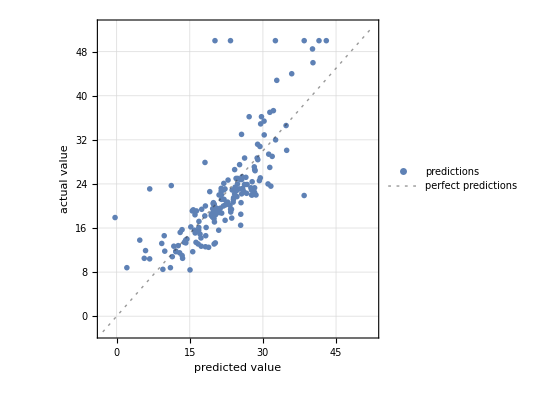

```mathematica
bhpm["ComparisonPlot"]
```

The predictor underestimates for low price and high price houses. 
It does better for houses with intermediate prices.

The residual plot is another way to see the differences between predicted and actual values of instances. Specifically, the residual plot gives the difference 

						Residuals = (actual value) - (predicted value)

for each instance. The residual plot for the test dataset looks as follows:

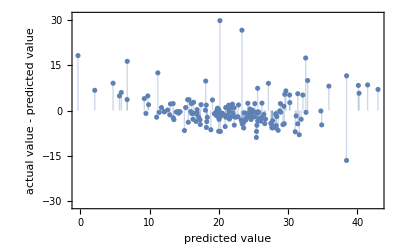

```mathematica
bhpm["ResidualPlot"]
```

One can also look at the numerical values of the residuals:

```mathematica
residuals=bhpm["Residuals"]
```

{-7.04819,6.49914,2.46007,-0.791437,-1.17825,0.607763,0.120731,-0.355411,-1.87935,3.95729,-4.49888,-1.88603,1.85103,1.40759,-0.428681,1.95988,5.16527,-0.899722,7.38689,-3.97153,0.504722,-1.80283,-0.869646,-0.822145,-2.16928,-2.85384,-0.847703,-1.71381,-3.4314,-8.02816,-5.78939,-4.7518,-4.90898,-0.550186,2.28873,-0.900971,-2.20761,-6.95695,-2.75073,-1.69113,0.995807,2.28946,0.989865,-1.65025,2.33624,-2.954,-0.889415,-0.41375,1.93813,-0.34116,-1.22463,4.84914,-0.920702,-5.32762,-4.22394,-4.40955,0.167411,11.5326,-4.346,-4.84294,0.877985,-3.43915,-1.78585,-2.65053,-4.67225,9.02389,5.57909,-0.153915,5.3653,2.63538,8.32937,8.49518,3.59229,12.5004,0.506459,-0.113255,-2.48248,-0.781503,-4.36811,-4.9953,-5.67452,-3.13918,-1.99012,-0.537145,9.95989,8.09188,-4.77266,-3.19125,-1.30379,-3.38932,-0.601693,5.73147,6.99492,5.14906,-2.32875,-2.97073,-1.12878,0.28246,-5.76766,-2.90238,-6.58006,-1.99281,-0.747734,-2.07618,-3.4754,-4.15304,-2.06722,-0.983483,-2.8423,-8.93351,2.29333,0.326841,-1.55374,2.39927,0.977311,2.12538,1.2674,3.50707,-16.558,16.3219,29.834,17.4436,26.6521,9.06461,-6.93856,-3.61525,6.71268,4.84578,-1.4164,-1.0023,-4.64128,-6.88837,-6.35984,-0.976195,5.97983,9.78547,18.2342,3.63784,-2.22291,-6.64425,-3.08946,-0.436768,-2.42465,-3.90145,-0.473996,0.17711,-3.01847,-0.610691,-0.336351,-5.61128,-2.87064,-2.25055,-5.79771,0.979839,-2.19824,1.80034,-2.26583,-0.192946,-2.11241,3.59562,2.73672,-1.66466,1.76408,-3.66706,-0.289153,0.756204,2.17554,-1.07885}

On average, the actual value of houses is higher than the predicted value:

```mathematica
Mean[residuals]
```

0.108265

This suggests that, on average, the predictor underestimates the price. However, we have seen above that the situation is slightly more complicated since under-prediction applies to houses with low and high prices.

In fact, looking at the standard deviation,

```mathematica
bhpm["StandardDeviation"]
```

5.7013

which gives an idea of the typical error of the prediction, we would conclude that a mean value of 0.1 cannot be taken as a significant difference between predicted and actual values of houses. Indeed, the prediction error is significantly larger than the mean value.

It is also interesting to look at the distribution of the residuals.  
It can be visualized by plotting a histogram:

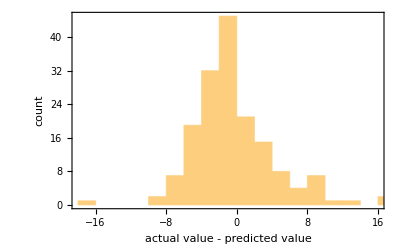

```mathematica
bhpm["ResidualHistogram"]
```

This histogram could also be obtained by applying the Histogram function on the residuals:

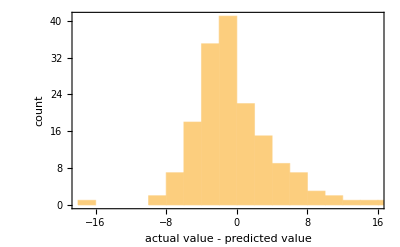

```mathematica
Histogram[residuals,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{"count",None},{"actual value - predicted value",None}},FrameTicks->All]
```

The peak of the histogram occurs for negative residuals. This corresponds to a large proportion of examples in for which (predicted value) > (actual value), i.e. it suggests an overestimate for some instances. Going back to the comparison and residual plots, we conclude that this corresponds to houses with intermediate prize. 

The histogram shows a pronounced tail towards positive residuals which corresponds to the underestimate of low and high prizes.

It is often interesting to identify worst predicted cases. Let us see the two worst predicted examples in this case:

```mathematica
Take[bhpm["WorstPredictedExamples"],2]
```

{{4.89822,0,18.1,0,0.631,4.97,100,1.3325,24,666,20.2,375.52,3.26}→50,{8.26725,0,18.1,1,0.668,5.875,89.6,1.1296,24,666,20.2,347.88,8.88}→50}

These are two houses that are worth $50,000. What are the predicted prizes?

```mathematica
bhp[Take[bhpm["WorstPredictedExamples"],2][[All,1]]]
```

{20.166,23.3479}